## Initial definitions

```mathematica
rep={kx->kp Cos[ϕ],ky->kp Sin[ϕ],kz-> kz};
rep1={kx->Subscript[k, x],ky->Subscript[k, y],kp->Subscript[k, p],Bx->B,v0->Subscript[v, 0],vz->Subscript[v, z], ϵsq->ϵ^2, ϵsqp->(ϵp)^2,cosg->Cos[γ],cosgp->Cos[γp],sing->Sin[γ],singp->Sin[γp],κt->κ̃,κtp->OverTilde[κp]};
ass=Assumptions->{kp,k0,ϵsq,ϵsqp,γ,θ,ϕ,v0,kx,ky,ϵ,kap,κt,κtp,κ,κp,kp,μ,Bx,e,vz}∈ Reals && v0>0 && kp>0  && k0>0 &&  κ>0  && k0>κ && 0<kap<k0 &&ϵ>0 && μ>0 && ϵ>κ && e>0 && ϵsq>0 && ϵsqp>0;
```

```mathematica
Clear[ham, en,eval, kr, v0, v, k0, Δ, λ,vz];
(* -Graphics- *)
d=v0{-kz Cos[ϕ],-kz Sin[ϕ], (√(kx^2+ky^2)-k0)}/.{κp->√(kx^2+ky^2)-k0,Cos[ϕ]->kx/(√(kx^2+ky^2)),Sin[ϕ]->ky/(√(kx^2+ky^2))};
ham =d[[1]]PauliMatrix[1]+d[[2]]PauliMatrix[2]+d[[3]]PauliMatrix[3];
{ev,evec}=FullSimplify[Eigensystem[ham],ass]
FullSimplify[(FullSimplify[{ev,evec}/.rep,ass]/.kp->k0+κp)/.kz^2->(ϵ/v0)^2-κp^2,ass]
```

{{-√(k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2) v0,√(k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2) v0},{{(-kx^2-ky^2+k0 √(kx^2+ky^2)+√((kx^2+ky^2) (k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2)))/((kx+ⅈ ky) kz),1},{-(kx^2+ky^2-k0 √(kx^2+ky^2)+√((kx^2+ky^2) (k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2)))/((kx+ⅈ ky) kz),1}}}

{{-ϵ,ϵ},{{(ⅇ^(-ⅈ ϕ) (ϵ/v0-κp))/kz,1},{-(ⅇ^(-ⅈ ϕ) (ϵ+v0 κp))/(kz v0),1}}}

```mathematica
k0^2+kp^2-2 k0 kp+kz^2==(kp-k0)^2+kz^2//FullSimplify
```

True

```mathematica
Print["zeroth order band velocity for +ve band:"];
FullSimplify[(FullSimplify[ Grad[ev[[2]],{kx,ky,kz}]/.rep,ass]/.kp->k0+κp)/.{k0->kp-κp,kz^2->(ϵ/v0)^2-κp^2},ass]
```

zeroth order band velocity for +ve band:

{(v0^2 κp Cos[ϕ])/ϵ,(v0^2 κp Sin[ϕ])/ϵ,(kz v0^2)/ϵ}

## for Bx

```mathematica
(*-Graphics-; -Graphics-*)
Print["BC vector:"];
bc=(- kz)/(2kp(√((k0-kp)^2+kz^2))^3){(kp-k0) Cos[ϕ],(kp-k0) Sin[ϕ],kz}/.{Cos[ϕ]->kx/(√(kx^2+ky^2)),Sin[ϕ]->ky/(√(kx^2+ky^2))};
FullSimplify[FullSimplify[bc/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2,ass]
Be={Bx,0,0};
Print["OMM vector:"];
omm=FullSimplify[e v0 √((k0-kp)^2+kz^2) bc/.kp->√(kx^2+ky^2),ass];
FullSimplify[FullSimplify[omm/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2,ass]
Print["OMM energy correction:"];
enomm=-omm.Be;
FullSimplify[enomm/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2
Print["OMM velocity, vomm:"];
velomm=FullSimplify[FullSimplify[Grad[enomm,{kx,ky,kz}]/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2,ass]/.{(k0-kp+kz) (-k0+kp+kz)->kz^2-(k0-kp)^2,(k0-kp-kz) (k0-kp+kz)->(k0-kp)^2-kz^2}
```

BC vector:

{((k0-kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^3),((k0-kp) kz v0^3 Sin[ϕ])/(2 kp ϵ^3),((k0-kp)^2 v0^3-v0 ϵ^2)/(2 kp ϵ^3)}

OMM vector:

{(e (k0-kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^2),(e (k0-kp) kz v0^3 Sin[ϕ])/(2 kp ϵ^2),(e (k0-kp)^2 v0^3-e v0 ϵ^2)/(2 kp ϵ^2)}

OMM energy correction:

(Bx e (-k0+kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^2)

OMM velocity, vomm:

{(Bx e kz v0^3 (kp (-(k0-kp)^2+kz^2) v0^2-(2 (k0-kp)^2 kp v0^2+(-2 k0+kp) ϵ^2) Cos[2 ϕ]))/(4 kp^2 ϵ^4),-(Bx e kz v0^3 (2 (k0-kp)^2 kp v0^2+(-2 k0+kp) ϵ^2) Sin[2 ϕ])/(4 kp^2 ϵ^4),-(Bx e (k0-kp) ((k0-kp)^2-kz^2) v0^5 Cos[ϕ])/(2 kp ϵ^4)}

```mathematica
(k0-kp+kz) (-k0+kp+kz)==-(k0-kp)^2+kz^2//FullSimplify
(k0-kp-kz) (k0-kp+kz)==(k0-kp)^2-kz^2//FullSimplify
```

True

True

```mathematica
{(Bx e kz v0^3 (kp (-(k0-kp)^2+kz^2) v0^2-(2 (k0-kp)^2 kp v0^2+(-2 k0+kp) ϵ^2) Cos[2 ϕ]))/(4 kp^2 ϵ^4),-(Bx e kz v0^3 (2 (k0-kp)^2 kp v0^2+(-2 k0+kp) ϵ^2) Sin[2 ϕ])/(4 kp^2 ϵ^4),-(Bx e (k0-kp) ((k0-kp)^2-kz^2) v0^5 Cos[ϕ])/(2 kp ϵ^4)}==(Bx e  v0^3)/(2 kp ϵ^4){kz(kp (-(k0-kp)^2+kz^2) v0^2-(2 (k0-kp)^2 kp v0^2+(-2 k0+kp) ϵ^2) Cos[2 ϕ])/(2 kp),-kz((2 (k0-kp)^2 kp v0^2+(-2 k0+kp) ϵ^2) Sin[2 ϕ])/(2 kp),-((k0-kp) ((k0-kp)^2-kz^2) v0^2 Cos[ϕ])/1}//FullSimplify
```

True

## for Bz

```mathematica
(*-Graphics-; -Graphics-*)
Print["BC vector:"];
bc=(- kz)/(2kp(√((k0-kp)^2+kz^2))^3){(kp-k0) Cos[ϕ],(kp-k0) Sin[ϕ],kz}/.{Cos[ϕ]->kx/(√(kx^2+ky^2)),Sin[ϕ]->ky/(√(kx^2+ky^2))};
FullSimplify[FullSimplify[bc/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2,ass]
Be={0,0,Bz};
Print["OMM vector:"];
omm=FullSimplify[e v0 √((k0-kp)^2+kz^2) bc/.kp->√(kx^2+ky^2),ass];
FullSimplify[FullSimplify[omm/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2,ass]
Print["OMM energy correction:"];
enomm=-omm.Be;
FullSimplify[enomm/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2
Print["OMM velocity, vomm:"];
velomm=FullSimplify[FullSimplify[Grad[enomm,{kx,ky,kz}]/.rep,ass]/.kz^2->ϵ^2/v0^2-(k0-kp)^2,ass]/.{(k0-kp+kz) (-k0+kp+kz)->kz^2-(k0-kp)^2,(k0-kp-kz) (k0-kp+kz)->(k0-kp)^2-kz^2}
```

BC vector:

{((k0-kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^3),((k0-kp) kz v0^3 Sin[ϕ])/(2 kp ϵ^3),((k0-kp)^2 v0^3-v0 ϵ^2)/(2 kp ϵ^3)}

OMM vector:

{(e (k0-kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^2),(e (k0-kp) kz v0^3 Sin[ϕ])/(2 kp ϵ^2),(e (k0-kp)^2 v0^3-e v0 ϵ^2)/(2 kp ϵ^2)}

OMM energy correction:

(Bz e v0^3 (-(k0-kp)^2+ϵ^2/v0^2))/(2 kp ϵ^2)

OMM velocity, vomm:

{(Bz e v0 (-k0 v0+kp v0-ϵ) (-k0 v0+kp v0+ϵ) (2 kp (-k0+kp) v0^2+ϵ^2) Cos[ϕ])/(2 kp^2 ϵ^4),(Bz e v0 (-k0 v0+kp v0-ϵ) (-k0 v0+kp v0+ϵ) (2 kp (-k0+kp) v0^2+ϵ^2) Sin[ϕ])/(2 kp^2 ϵ^4),(Bz e (k0-kp)^2 kz v0^5)/(kp ϵ^4)}

## Fermi surface eqn

```mathematica
(* OMM en corr *)
FullSimplify[{(Bx e (-k0+kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^2),(Bz e v0^3 (-(k0-kp)^2+ϵ^2/v0^2))/(2 kp ϵ^2)}/.{kp->κ Cos[γ]+k0,kz->κ Sin[γ],ϵ->v0 κ},ass]
```

{(Bx e v0 Cos[γ] Cos[ϕ] Sin[γ])/(2 k0+2 κ Cos[γ]),(Bz e v0 Sin[γ]^2)/(2 k0+2 κ Cos[γ])}

```mathematica
(* ϵ=v0 √((k0-kp)^2+kz^2) *)
Clear[sol];
sol=FullSimplify[Flatten[SolveValues[v0 κ+(Bz e v0 Sin[γ]^2)/(2 k0+2 κ Cos[γ])==μ,κ],1],ass]
```

{(μ-Sec[γ] (k0 v0+√((k0 v0+μ Cos[γ])^2-2 Bz e v0^2 Cos[γ] Sin[γ]^2)))/(2 v0),(μ+Sec[γ] (-k0 v0+√((k0 v0+μ Cos[γ])^2-2 Bz e v0^2 Cos[γ] Sin[γ]^2)))/(2 v0)}

### checking FS distortion

```mathematica
Clear[ener,Bz,ifun];

ener[Bz_,μ_,{v0_,k0_},γ_]:=Block[{e=1},

{(μ-Sec[γ] (k0 v0+√((k0 v0+μ Cos[γ])^2-2 Bz e v0^2 Cos[γ] Sin[γ]^2)))/(2 v0),(μ+Sec[γ] (-k0 v0+√((k0 v0+μ Cos[γ])^2-2 Bz e v0^2 Cos[γ] Sin[γ]^2)))/(2 v0)}
];
```

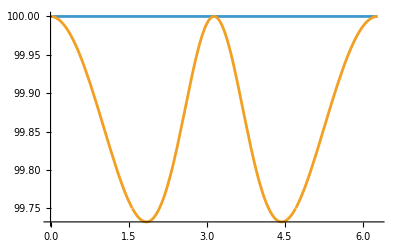

```mathematica
mu=0.04;k0val=200;Bzval=100;v0val=0.0004;
Plot[{mu/v0val,ener[Bzval,mu,{v0val,k0val},γ][[2]]},{γ,0,2π},PlotRange->All]
```

```mathematica
FullSimplify[(Bz e v0^3 (-(k0-kp)^2+ϵ^2/v0^2))/(2 kp ϵ^2)/.{ϵ->√(k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2) v0,kp->√(kx^2+ky^2)},ass]
```

```mathematica
lim=500;
c0=ContourPlot3D[{√(k0val^2+kx^2+ky^2-2 k0val √(kx^2+ky^2)+kz^2) v0val==mu},{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},Mesh->None,ContourStyle-> {Directive[Opacity[1],Cyan]},AxesLabel->{"k_x","k_y","k_z"}];
cmod=ContourPlot3D[{(k0val^2+kx^2+ky^2-2 k0val √(kx^2+ky^2)+kz^2 )v0val^2==(mu-(Bzval kz^2 v0val)/(2 √(kx^2+ky^2) (k0val^2+kx^2+ky^2-2 k0val √(kx^2+ky^2)+kz^2)))^2},{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},ContourStyle-> {Directive[Opacity[1],Cyan]},AxesLabel->{"k_x","k_y","k_z"},Mesh->None]//Quiet;
{c0,cmod}
```

{-Graphics3D-,-Graphics3D-}

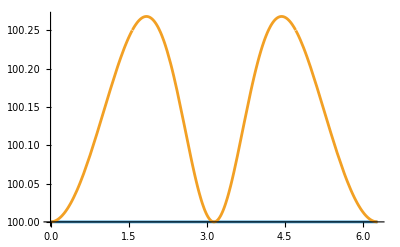

{c0,-Graphics3D-}

```mathematica
mu=0.04;k0val=200;Bzval=-100;v0val=0.0004;
Plot[{mu/v0val,ener[Bzval,mu,{v0val,k0val},γ][[2]]},{γ,0,2π},PlotRange->All]
lim=500;
cmod=ContourPlot3D[{(k0val^2+kx^2+ky^2-2 k0val √(kx^2+ky^2)+kz^2 )v0val^2==(mu-(Bzval kz^2 v0val)/(2 √(kx^2+ky^2) (k0val^2+kx^2+ky^2-2 k0val √(kx^2+ky^2)+kz^2)))^2},{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},ContourStyle-> {Directive[Opacity[1],Cyan]},AxesLabel->{"k_x","k_y","k_z"},Mesh->None]//Quiet;
{c0,cmod}
```

## Computing W_kk'

```mathematica
(* eigensystem: {{-ϵ,ϵ},{{(ⅇ^(-ⅈ ϕ) (ϵ/v0-κp))/kz,1},{-(ⅇ^(-ⅈ ϕ) (ϵ+v0 κp))/(kz v0),1}}} *)
```

```mathematica
Clear[vecp,vecpdag,vecm,vecmdag];
vecm[γ_,ϕ_]={Sin[γ/2], ⅇ^(ⅈ ϕ) Cos[γ/2]};
vecmdag[γ_,ϕ_]={Sin[γ/2], ⅇ^(-ⅈ ϕ) Cos[γ/2]};
(*normm=*)FullSimplify[vecmdag[γ,ϕ].vecm[γ,ϕ],ass]
vecp[γ_,ϕ_]={ Cos[γ/2],- ⅇ^(ⅈ ϕ) Sin[γ/2]};
vecpdag[γ_,ϕ_]={ Cos[γ/2],- ⅇ^(-ⅈ ϕ) Sin[γ/2]};
(*normp=*)FullSimplify[vecpdag[γ,ϕ].vecp[γ,ϕ],ass]
```

1

1

```mathematica
TeXForm[{-ⅇ^(-ⅈ ϕ) Sin[θ/2],Cos[θ/2]}]
```

```mathematica
FullSimplify[((vecpdag[γ,ϕ].vecp[γp,ϕp])(vecpdag[γp,ϕp].vecp[γ,ϕ]))/1,ass]
1/(2π)Integrate[%,{ϕp,0,2π}]//FullSimplify
```

1/2 (1+Cos[γ] Cos[γp]+Cos[ϕ-ϕp] Sin[γ] Sin[γp])

1/2 (1+Cos[γ] Cos[γp])

## sigma

```mathematica
repl={kx->(k0+κ Cos[γ]) Cos[ϕ],ky->(k0+κ Cos[γ])Sin[ϕ],kz-> κ Sin[γ],κp-> κ Cos[γ],ϵ->v0 κ, kp->k0+κ Cos[γ]};
	(* BC= {((k0-kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^3),((k0-kp) kz v0^3 Sin[ϕ])/(2 kp ϵ^3),((k0-kp)^2 v0^3-v0 ϵ^2)/(2 kp ϵ^3)}=*)

Print["BC:"];FullSimplify[{(-κp kz v0^3 Cos[ϕ])/(2 kp ϵ^3),(-κp kz v0^3 Sin[ϕ])/(2 kp ϵ^3),(κp^2 v0^3-v0 ϵ^2)/(2 kp ϵ^3)}/.repl,ass]==-1/(2κ( k0 +κ Cos[γ])){(Sin[2 γ] Cos[ϕ])/2,(Sin[2 γ] Sin[ϕ])/2,Sin[γ]^2}//FullSimplify
Print["OMM:"];
FullSimplify[{(e (k0-kp) kz v0^3 Cos[ϕ])/(2 kp ϵ^2),(e (k0-kp) kz v0^3 Sin[ϕ])/(2 kp ϵ^2),(e (k0-kp)^2 v0^3-e v0 ϵ^2)/(2 kp ϵ^2)}/.repl,ass]
Print["v0vec:"];
FullSimplify[ {(v0^2 κp Cos[ϕ])/ϵ,(v0^2 κp Sin[ϕ])/ϵ,(kz v0^2)/ϵ}/.repl,ass]
Print["vommvec:"];
FullSimplify[{(Bz e v0 (-k0 v0+kp v0-ϵ) (-k0 v0+kp v0+ϵ) (2 kp (-k0+kp) v0^2+ϵ^2) Cos[ϕ])/(2 kp^2 ϵ^4),(Bz e v0 (-k0 v0+kp v0-ϵ) (-k0 v0+kp v0+ϵ) (2 kp (-k0+kp) v0^2+ϵ^2) Sin[ϕ])/(2 kp^2 ϵ^4),(Bz e (k0-kp)^2 kz v0^5)/(kp ϵ^4)}/.repl,ass]/.{Bz->B,κ->kf1[γ]}
Print["vomm.k:"];
FullSimplify[{(Bz e v0 (-k0 v0+kp v0-ϵ) (-k0 v0+kp v0+ϵ) (2 kp (-k0+kp) v0^2+ϵ^2) Cos[ϕ])/(2 kp^2 ϵ^4),(Bz e v0 (-k0 v0+kp v0-ϵ) (-k0 v0+kp v0+ϵ) (2 kp (-k0+kp) v0^2+ϵ^2) Sin[ϕ])/(2 kp^2 ϵ^4),(Bz e (k0-kp)^2 kz v0^5)/(kp ϵ^4)}/.repl,ass]
```

BC:

True

OMM:

{-(e v0 Cos[ϕ] Sin[2 γ])/(4 (k0+κ Cos[γ])),-(e v0 Sin[2 γ] Sin[ϕ])/(4 (k0+κ Cos[γ])),-(e v0 Sin[γ]^2)/(2 (k0+κ Cos[γ]))}

v0vec:

{v0 Cos[γ] Cos[ϕ],v0 Cos[γ] Sin[ϕ],v0 Sin[γ]}

vommvec:

{-(B e v0 Cos[ϕ] (2 k0 Cos[γ]+(2+Cos[2 γ]) kf1[γ]) Sin[γ]^2)/(2 kf1[γ] (k0+Cos[γ] kf1[γ])^2),-(B e v0 (2 k0 Cos[γ]+(2+Cos[2 γ]) kf1[γ]) Sin[γ]^2 Sin[ϕ])/(2 kf1[γ] (k0+Cos[γ] kf1[γ])^2),(B e v0 Cos[γ]^2 Sin[γ])/(kf1[γ] (k0+Cos[γ] kf1[γ]))}

vomm.k:

{-(Bz e v0 (2 k0 Cos[γ]+κ (2+Cos[2 γ])) Cos[ϕ] Sin[γ]^2)/(2 κ (k0+κ Cos[γ])^2),-(Bz e v0 (2 k0 Cos[γ]+κ (2+Cos[2 γ])) Sin[γ]^2 Sin[ϕ])/(2 κ (k0+κ Cos[γ])^2),(Bz e v0 Cos[γ]^2 Sin[γ])/(κ (k0+κ Cos[γ]))}

```mathematica
Clear[sig,s,k0,v0,μ,B,v0];
sig[B_,μ_,k0_,v0_,βintra_]:=Block[{e=1,vtot1,cond,matr,bc1,γ,τ1,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,cs,λ1,a1,cost,γp,Dphase1,h1,vz1,zero1,cg1,cgcg1,hzero1,hcg1,hstcp1,hstsp1,colvec,mat,sol,sol1,Λ1,s1,int1,z0,c0,rvec},

kf1[γ_]=(μ+Sec[γ] (-k0 v0+√((k0 v0+μ Cos[γ])^2-2 B e v0^2 Cos[γ] Sin[γ]^2)))/(2 v0);
bc1[γ_]=-1/(2kf1[γ]( k0 + kf1[γ]Cos[γ])){(Sin[2 γ] Cos[ϕ])/2,(Sin[2 γ] Sin[ϕ])/2,Sin[γ]^2};
Dphase1[γ_]=1 +e {0,0,B}.bc1[γ] (*-Graphics-*);
vvec1[γ_]=v0{ Cos[γ] Cos[ϕ], Cos[γ] Sin[ϕ], Sin[γ]};
vmm1[γ_]={-(B e v0 Cos[ϕ] (2 k0 Cos[γ]+(2+Cos[2 γ]) kf1[γ]) Sin[γ]^2)/(2 kf1[γ] (k0+Cos[γ] kf1[γ])^2),-(B e v0 (2 k0 Cos[γ]+(2+Cos[2 γ]) kf1[γ]) Sin[γ]^2 Sin[ϕ])/(2 kf1[γ] (k0+Cos[γ] kf1[γ])^2),(B e v0 Cos[γ]^2 Sin[γ])/(kf1[γ] (k0+Cos[γ] kf1[γ]))};
vtot1[γ_]=vvec1[γ]+vmm1[γ];
vdotk1[γ_]=kf1[γ]{Cos[γ] Cos[ϕ],Cos[γ] Sin[ϕ],Sin[γ]}.vtot1[γ];

h1[γ_]=1/Dphase1[γ]((**)( vtot1[γ])[[3]]+ e B(bc1[γ].(vtot1[γ]))(**) );
(* -Graphics- ; -Graphics-*)
(*****************)
τ1[γ_]=(βintra/2 NIntegrate [((kf1[γp])^2(kf1[γp] Cos[γp]+k0))/Abs[vdotk1[γp]] Dphase1[γp],{γp,0,2π}]+
(βintra   Cos[γ])/2 NIntegrate [((kf1[γp])^2(kf1[γp]Cos[γp] +k0))/Abs[vdotk1[γp]] Dphase1[γp]Cos[γp],{γp,0,2π}])^-1;

(******************)
f1[γ_]=((kf1[γ])^2(kf1[γ]  Cos[γ]+k0))/Abs[vdotk1[γ]] Dphase1[γ] τ1[γ];
zero1=Quiet[NIntegrate [f1[γp],{γp,0,2π}]];
cg1=Quiet[NIntegrate [f1[γp] Cos[γp],{γp,0,2π}]];
cgcg1=Quiet[NIntegrate [f1[γp] Cos[γp]^2,{γp,0,2π}]];
hzero1=Quiet[NIntegrate [f1[γp] h1[γp],{γp,0,2π}]];
hcg1=Quiet[NIntegrate [f1[γp]h1[γp]Cos[γp],{γp,0,2π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hcg1 βintra}});
mat=({{1-(zero1 βintra)/2, -(cg1 βintra)/2}, {-(cg1 βintra)/2, 1-(cgcg1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 cg1;
sol=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
(* choosing wrong matrix elements above give wrong solns; choice can be fixed by the answer from sig0 below *)
Λ1[γ_]=(λ1-h1[γ]+a1 Cos[γ])/.sol;
int1[γ_]=-f1[γ]h1[γ]Λ1[γ];
cond=Quiet[NIntegrate[int1[γ],{γ,0,2π}]];

{B,cond(*,MatrixRank[mat,Tolerance->10^(-4)]*)}
];
(* sig[B_,μ_,k0_,v0_,βintra_] *)
mu=0.1;k0val=4;Bzval=1;v0val=1;
ampli=0.1;
sig[Bzval,mu,k0val,v0val,ampli]//Quiet
```

{1,12.5091}

## sigma at B=0

```mathematica
Clear[sig0,s,k0,v0,μ,B,v0];
sig0[μ_,k0_,v0_,βintra_]:=Block[{e=1,vtot1,cond,matr,bc1,γ,τ1,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,cs,λ1,a1,cost,γp,Dphase1,h1,vz1,zero1,cg1,cgcg1,hzero1,hcg1,hstcp1,hstsp1,colvec,mat,sol,sol1,Λ1,s1,int1},

kf1[γ_]=μ/v0;
bc1[γ_]=-1/(2kf1[γ]( k0 + kf1[γ]Cos[γ])){(Sin[2 γ] Cos[ϕ])/2,(Sin[2 γ] Sin[ϕ])/2,Sin[γ]^2};
Dphase1[γ_]=1 ;
vvec1[γ_]=v0{ Cos[γ] Cos[ϕ], Cos[γ] Sin[ϕ], Sin[γ]};
vmm1[γ_]={0,0,0};
vtot1[γ_]=vvec1[γ]+vmm1[γ];
vdotk1[γ_]=kf1[γ]{Cos[γ] Cos[ϕ],Cos[γ] Sin[ϕ],Sin[γ]}.vtot1[γ];

h1[γ_]=1/Dphase1[γ]( vtot1[γ])[[3]];
(* -Graphics- ; -Graphics-*)
(*****************)
τ1[γ_]=(βintra/2 NIntegrate [((kf1[γp])^2(kf1[γp] Cos[γp]+k0))/Abs[vdotk1[γp]] Dphase1[γp],{γp,0,2π}]+
(βintra   Cos[γ])/2 NIntegrate [((kf1[γp])^2(kf1[γp]Cos[γp] +k0))/Abs[vdotk1[γp]] Dphase1[γp]Cos[γp],{γp,0,2π}])^-1;

(******************)
f1[γ_]=((kf1[γ])^2(kf1[γ]  Cos[γ]+k0))/Abs[vdotk1[γ]] Dphase1[γ] τ1[γ];
zero1=Quiet[NIntegrate [f1[γp],{γp,0,2π}]];
cg1=Quiet[NIntegrate [f1[γp] Cos[γp],{γp,0,2π}]];
cgcg1=Quiet[NIntegrate [f1[γp] Cos[γp]^2,{γp,0,2π}]];
hzero1=Quiet[NIntegrate [f1[γp] h1[γp],{γp,0,2π}]];
hcg1=Quiet[NIntegrate [f1[γp]h1[γp]Cos[γp],{γp,0,2π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hcg1 βintra}});
mat=({{1-(zero1 βintra)/2, -(cg1 βintra)/2}, {-(cg1 βintra)/2, 1-(cgcg1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 cg1;
sol=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
(* choosing wrong matrix elements above give wrong solns; choice can be fixed by the answer from sig0 below *)
Λ1[γ_]=(λ1-h1[γ]+a1 Cos[γ])/.sol;
int1[γ_]=-f1[γ]h1[γ]Λ1[γ];
cond=Quiet[NIntegrate[int1[γ],{γ,0,2π}]];
(*{cond,MatrixRank[mat,Tolerance->10^(-4)]}*)
cond
];
(* sig[B_,μ_,k0_,v0_,βintra_] *)
mu=0.1;k0val=100;Bzval=1;v0val=1;
ampli=0.1;
sig0[mu,k0val,v0val,ampli]//Quiet
```

10.

## Plots

```mathematica
(* -Graphics- *)
```

```mathematica
mu=0.04;k0val=200;v0val=0.0004;ampli=1;
sub=sig0[mu,k0val,v0val,ampli]
dat1=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-10.3,10.3,1}];
dat2=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-100,100,10}];
list=Sort[Join[dat1,dat2]]
```

```mathematica
list={{-100,1.5742538935993914*^-7},{-90,1.574247247453025*^-7},{-80,1.5742405878696872*^-7},{-70,1.574233914882535*^-7},{-60,1.5742272285247452*^-7},{-50,1.5742205288295137*^-7},{-40,1.5742138158300534*^-7},{-30,1.5742070895595992*^-7},{-20,1.574200350051402*^-7},{-10.3,1.574193800111924*^-7},{-10,1.5741935973387357*^-7},{-9.3,1.5741931241552028*^-7},{-8.3,1.5741924480667927*^-7},{-7.300000000000001,1.5741917718467282*^-7},{-6.300000000000001,1.574191095495042*^-7},{-5.300000000000001,1.5741904190117662*^-7},{-4.300000000000001,1.5741897423969362*^-7},{-3.3000000000000007,1.5741890656505837*^-7},{-2.3000000000000007,1.574188388772743*^-7},{-1.3000000000000007,1.5741877117634456*^-7},{-0.3000000000000007,1.5741870346227283*^-7},{0,1.5741868313920584*^-7},{0.6999999999999993,1.574186357350621*^-7},{1.6999999999999993,1.5741856799471587*^-7},{2.6999999999999993,1.5741850024123745*^-7},{3.6999999999999993,1.5741843247463025*^-7},{4.699999999999999,1.574183646948974*^-7},{5.699999999999999,1.5741829690204234*^-7},{6.699999999999999,1.5741822909606838*^-7},{7.699999999999999,1.5741816127697886*^-7},{8.7,1.5741809344477711*^-7},{9.7,1.5741802559946658*^-7},{10,1.5741800524331763*^-7},{20,1.5741732603069248*^-7},{30,1.5741664551094853*^-7},{40,1.5741596368742267*^-7},{50,1.5741528056345399*^-7},{60,1.5741459614238314*^-7},{70,1.574139104275533*^-7},{80,1.5741322342230934*^-7},{90,1.5741253512999832*^-7},{100,1.5741184555396913*^-7}};
len=Length[list];
sc=1/(1.5741868313920584*^-7);
mult=10^5;
d1=Table[{list[[i,1]],(Re[list[[i,2]]]sc-1)mult},{i,1,len}];
ListLinePlot[d1];
```

```mathematica
mu=0.01;k0val=200;v0val=0.0004;ampli=1;
sub=sig0[mu,k0val,v0val,ampli]
dat1=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-10.3,10.3,1}];
dat2=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-100,100,10}];
list=Sort[Join[dat1,dat2]]
```

1.59843×10^-7

```mathematica
list={{-100,1.5984683634876558*^-7},{-90,1.598463358398135*^-7},{-80,1.5984587064240577*^-7},{-70,1.598454409528799*^-7},{-60,1.5984504696869766*^-7},{-50,1.5984468888845105*^-7},{-40,1.5984436691187045*^-7},{-30,1.5984408123983406*^-7},{-20,1.5984383207437247*^-7},{-10.3,1.598436254562734*^-7},{-10,1.598436196186793*^-7},{-9.3,1.5984360612683541*^-7},{-8.3,1.598435871666814*^-7},{-7.300000000000001,1.5984356857601634*^-7},{-6.300000000000001,1.5984355035504532*^-7},{-5.300000000000001,1.5984353250397363*^-7},{-4.300000000000001,1.5984351502300713*^-7},{-3.3000000000000007,1.5984349791235093*^-7},{-2.3000000000000007,1.5984348117221102*^-7},{-1.3000000000000007,1.5984346480279313*^-7},{-0.3000000000000007,1.598434488043031*^-7},{0,1.5984344407711272*^-7},{0.6999999999999993,1.5984343317694647*^-7},{1.6999999999999993,1.5984341792093042*^-7},{2.6999999999999993,1.5984340303646063*^-7},{3.6999999999999993,1.5984338852374344*^-7},{4.699999999999999,1.5984337438298578*^-7},{5.699999999999999,1.5984336061439354*^-7},{6.699999999999999,1.598433472181742*^-7},{7.699999999999999,1.5984333419453465*^-7},{8.7,1.5984332154368102*^-7},{9.7,1.5984330926582156*^-7},{10,1.598433056552282*^-7},{20,1.5984320455973794*^-7},{30,1.5984314099856763*^-7},{40,1.5984311518084006*^-7},{50,1.598431273168885*^-7},{60,1.598431776182642*^-7},{70,1.5984326629774581*^-7},{80,1.5984339356934768*^-7},{90,1.598435596483272*^-7},{100,1.598437647511948*^-7}};
len=Length[list];
sc=1/(1.5984344407711272*^-7);
mult=10^5;
d2=Table[{list[[i,1]],(Re[list[[i,2]]]sc-1)mult},{i,1,len}];
ListLinePlot[d2];
```

```mathematica
mu=0.04;k0val=200;v0val=0.0004;ampli=0.01;
sub=sig0[mu,k0val,v0val,ampli]
dat1=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-10.3,10.3,1}];
dat2=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-100,100,10}];
list=Sort[Join[dat1,dat2]]
```

0.0000157419

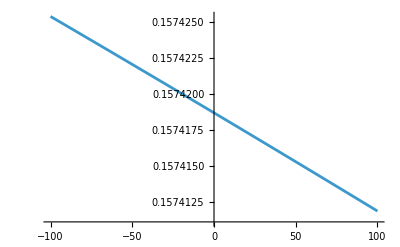

```mathematica
list={{-100,0.000015742538935993912},{-90,0.00001574247247453025},{-80,0.00001574240587869687},{-70,0.000015742339148825346},{-60,0.00001574227228524745},{-50,0.000015742205288295138},{-40,0.000015742138158300534},{-30,0.000015742070895595986},{-20,0.00001574200350051402},{-10.3,0.000015741938001119235},{-10,0.00001574193597338736},{-9.3,0.00001574193124155203},{-8.3,0.000015741924480667926},{-7.300000000000001,0.000015741917718467287},{-6.300000000000001,0.00001574191095495042},{-5.300000000000001,0.000015741904190117656},{-4.300000000000001,0.000015741897423969363},{-3.3000000000000007,0.000015741890656505844},{-2.3000000000000007,0.00001574188388772744},{-1.3000000000000007,0.000015741877117634458},{-0.3000000000000007,0.000015741870346227282},{0,0.000015741868313920583},{0.6999999999999993,0.000015741863573506213},{1.6999999999999993,0.000015741856799471592},{2.6999999999999993,0.00001574185002412374},{3.6999999999999993,0.000015741843247463023},{4.699999999999999,0.00001574183646948974},{5.699999999999999,0.00001574182969020423},{6.699999999999999,0.000015741822909606835},{7.699999999999999,0.00001574181612769789},{8.7,0.000015741809344477712},{9.7,0.00001574180255994666},{10,0.000015741800524331764},{20,0.00001574173260306925},{30,0.00001574166455109485},{40,0.00001574159636874227},{50,0.0000157415280563454},{60,0.000015741459614238318},{70,0.000015741391042755323},{80,0.000015741322342230938},{90,0.00001574125351299983},{100,0.000015741184555396905}};
len=Length[list];
sc=1(*/(0.000015741868313920583)*);
mult=10^4;
d3=Table[{list[[i,1]],(Re[list[[i,2]]]sc-0)mult},{i,1,len}];
ListLinePlot[d3]
```

```mathematica
mu=0.01;k0val=200;v0val=0.0004;ampli=0.1;
sub=sig0[mu,k0val,v0val,ampli]
dat1=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-10.3,10.3,1}];
dat2=Table[Quiet[sig[B,mu,k0val,v0val,ampli]],{B,-100,100,10}];
list=Sort[Join[dat1,dat2]]
```

1.59843×10^-6

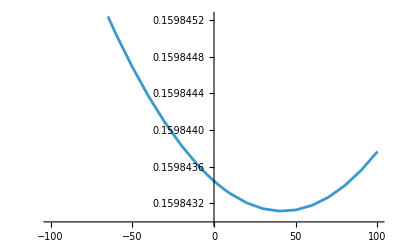

```mathematica
list={{-100,1.598468363487656*^-6},{-90,1.598463358398135*^-6},{-80,1.5984587064240568*^-6},{-70,1.5984544095287994*^-6},{-60,1.5984504696869761*^-6},{-50,1.59844688888451*^-6},{-40,1.5984436691187042*^-6},{-30,1.5984408123983408*^-6},{-20,1.5984383207437247*^-6},{-10.3,1.598436254562734*^-6},{-10,1.5984361961867926*^-6},{-9.3,1.5984360612683543*^-6},{-8.3,1.5984358716668138*^-6},{-7.300000000000001,1.5984356857601627*^-6},{-6.300000000000001,1.5984355035504532*^-6},{-5.300000000000001,1.5984353250397364*^-6},{-4.300000000000001,1.5984351502300713*^-6},{-3.3000000000000007,1.5984349791235096*^-6},{-2.3000000000000007,1.5984348117221104*^-6},{-1.3000000000000007,1.598434648027931*^-6},{-0.3000000000000007,1.5984344880430312*^-6},{0,1.5984344407711272*^-6},{0.6999999999999993,1.5984343317694646*^-6},{1.6999999999999993,1.598434179209304*^-6},{2.6999999999999993,1.5984340303646066*^-6},{3.6999999999999993,1.5984338852374341*^-6},{4.699999999999999,1.5984337438298567*^-6},{5.699999999999999,1.5984336061439356*^-6},{6.699999999999999,1.5984334721817418*^-6},{7.699999999999999,1.5984333419453467*^-6},{8.7,1.59843321543681*^-6},{9.7,1.5984330926582157*^-6},{10,1.5984330565522814*^-6},{20,1.598432045597379*^-6},{30,1.5984314099856773*^-6},{40,1.5984311518084005*^-6},{50,1.5984312731688853*^-6},{60,1.5984317761826424*^-6},{70,1.598432662977458*^-6},{80,1.5984339356934762*^-6},{90,1.5984355964832714*^-6},{100,1.598437647511948*^-6}};
len=Length[list];
sc=1(*/(1.5984344407711272*^-6)*);
mult=10^5;
d4=Table[{list[[i,1]],(Re[list[[i,2]]]sc-0)mult},{i,1,len}];
ListLinePlot[d4]
```

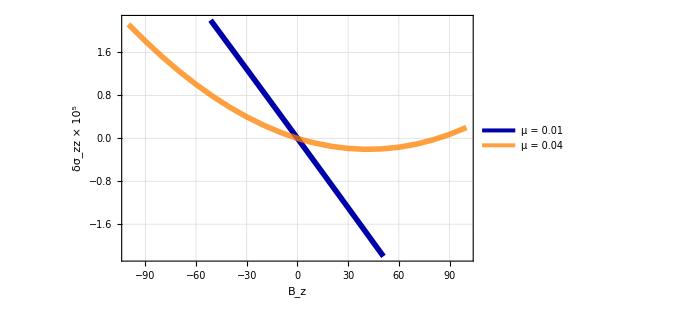

```mathematica
thk=0.007;
style={(**)Directive[Darker[Blue],Thickness[0.008]],(**)Directive[Orange,Thickness[0.008],Opacity[0.75]](***),Directive[Darker[Red],Thickness[0.008],Dashed]};

pl=ListLinePlot[{d1,d2},PlotStyle->style,PlotRange->{-2.2,2.2},GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz × 10^5"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->500,PlotLegends->Placed[LineLegend[{"μ = 0.01","μ = 0.04"},LabelStyle->{FontFamily->"Times",20,Bold,Darker[Gray]},LegendLayout->"Row"],(*{Scaled[{0.5,0.8}], {-0.3, 0.6}}*)Below]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["vnr-sigz.pdf",Rasterize[pl,Background->None],ImageResolution->100];
```